```mathematica
Union[Range[261.,264.,.5],Range[264.,264.5,.1],{264.5,264.55,264.6,264.65,264.67},Range[264.7,264.8,.05],Range[264.8,265.5,.1],Range[266.,270.,1]]
```

{261.,261.5,262.,262.5,263.,263.5,264.,264.1,264.2,264.3,264.4,264.5,264.55,264.6,264.65,264.67,264.7,264.75,264.8,264.9,265.,265.1,265.2,265.3,265.4,265.5,266.,267.,268.,269.,270.}

```mathematica
{.108,.123,.143,.173,.218,.300,.488,.559,.655,.785,.983,1.286,1.483,1.670,1.787,1.804,1.799,1.730,1.610,1.324,1.061,.859,.703,.602,.517,.452,.272,.145,.096,.070,.053}
```

{0.108,0.123,0.143,0.173,0.218,0.3,0.488,0.559,0.655,0.785,0.983,1.286,1.483,1.67,1.787,1.804,1.799,1.73,1.61,1.324,1.061,0.859,0.703,0.602,0.517,0.452,0.272,0.145,0.096,0.07,0.053}

```mathematica
Transpose@{%13,%18}
```

{{261.,0.108},{261.5,0.123},{262.,0.143},{262.5,0.173},{263.,0.218},{263.5,0.3},{264.,0.488},{264.1,0.559},{264.2,0.655},{264.3,0.785},{264.4,0.983},{264.5,1.286},{264.55,1.483},{264.6,1.67},{264.65,1.787},{264.67,1.804},{264.7,1.799},{264.75,1.73},{264.8,1.61},{264.9,1.324},{265.,1.061},{265.1,0.859},{265.2,0.703},{265.3,0.602},{265.4,0.517},{265.5,0.452},{266.,0.272},{267.,0.145},{268.,0.096},{269.,0.07},{270.,0.053}}

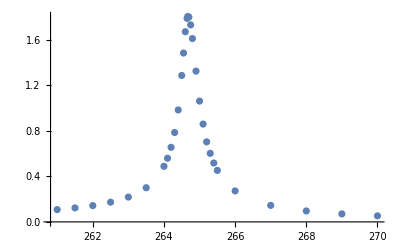

```mathematica
ListPlot[%19]
```

```mathematica
FindFit[%19,A/(ω0 √(1+Q^2(ω/ω0-ω0/ω)^2)),{A,ω0,Q},ω]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{A→2.00416,ω0→8.63275×10^-8,Q→0.346842}

```mathematica
FindFit[%19,A/(ω0 √(1+Q^2(ω/ω0-ω0/ω)^2))/.ω0->264.67,{A,Q},ω]
```

{A→476.964,Q→643.393}

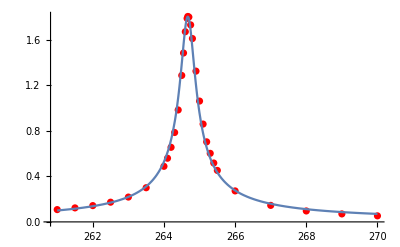

```mathematica
Show[ListPlot[%19,PlotStyle->Red],Plot[A/(ω0 √(1+Q^2 (ω/ω0-ω0/ω)^2))/.ω0->264.67/.{A->476.9636861326582,Q->643.3925382262146},{ω,261.,270.},PlotRange->All]]
```

```mathematica
FindFit[%19,{A/(ω0 √(1+Q^2(ω/ω0-ω0/ω)^2)),264.6<ω0<264.75,Q>0},{A,Q,ω0},ω]
```

{A→481.415,Q→649.886,ω0→264.702}

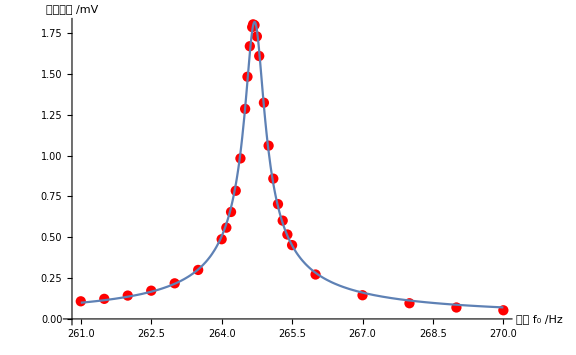

```mathematica
Show[ListPlot[%19,PlotStyle->Red],Plot[{A/(ω0 √(1+Q^2 (ω/ω0-ω0/ω)^2))(*,264.6<ω0<264.75*)}/.{A->481.4151198431628,Q->-649.8862992864576,ω0->264.7018103602856},{ω,261.,270.},PlotRange->All],AxesLabel->{"频率 f_0\n/Hz","相对振幅\n/mV"},ImageSize->Large]
```

```mathematica
Transpose@{2Drop[Range[0,35,5],{3}],{3.77,4.40,5.50,5.48,5.93,6.48,7.0}}
```

{{0,3.77},{10,4.4},{30,5.5},{40,5.48},{50,5.93},{60,6.48},{70,7.}}

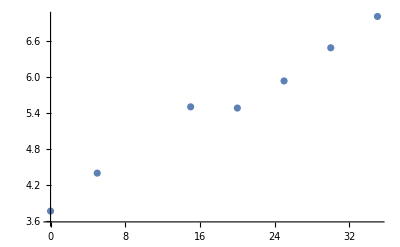

```mathematica
ListPlot[{{0,3.77},{5,4.4},{15,5.5},{20,5.48},{25,5.93},{30,6.48},{35,7.}}]
```

```mathematica
Transpose@{Drop[Range[0,35,5],{3}],{3.77,4.40,5.50,5.48,5.93,6.48,7.0}^2}
```

{{0,14.2129},{5,19.36},{15,30.25},{20,30.0304},{25,35.1649},{30,41.9904},{35,49.}}

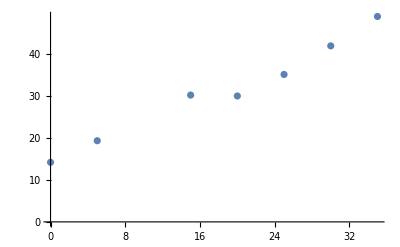

```mathematica
ListPlot[{{0,14.2129},{5,19.360000000000003},{15,30.25},{20,30.030400000000004},{25,35.164899999999996},{30,41.99040000000001},{35,49.}}(*,Joined->True*)]
```

```mathematica
Transpose@{Range[0,35,5],{3.77,4.40,5.05,5.50,5.48,5.93,6.48,7.0}^2}
```

{{0,14.2129},{5,19.36},{10,25.5025},{15,30.25},{20,30.0304},{25,35.1649},{30,41.9904},{35,49.}}

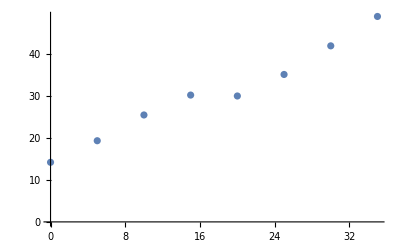

```mathematica
ListPlot[{{0,14.2129},{5,19.360000000000003},{10,25.502499999999998},{15,30.25},{20,30.030400000000004},{25,35.164899999999996},{30,41.99040000000001},{35,49.}}]
```

```mathematica
FindFit[%58,(4 π^2)/k(m0+mx),{m0,k},mx]
```

{m0→89.6705,k→908.837}

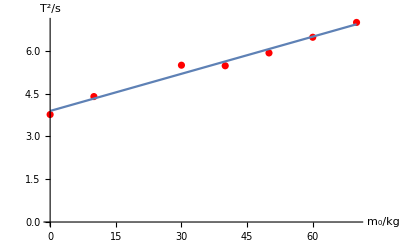

```mathematica
Show[ListPlot[%58,PlotStyle->Red,PlotRange->{0,All}],Plot[((4 π^2) (m0+mx))/k/.{m0->89.67053132037701,k->908.836705213333},{mx,0,70}],AxesLabel->{"m_0/kg","T^2/s"}]
```

```mathematica
0.04343840579710146 (89.67053132037701+mx)==5.05
```

0.0434384 (89.6705+mx)==5.05

```mathematica
Solve[0.04343840579710146 (89.67053132037701+mx)==5.05,{mx}]
```

{{mx→26.586}}

```mathematica
Sort@Union[Range[263.,264.,.5],Range[264.,265,.1],{264.55},Range[265.,266.,.5]]
```

{263.,263.5,264.,264.1,264.2,264.3,264.4,264.5,264.55,264.6,264.7,264.8,264.9,265.,265.5,266.}

```mathematica
{.235,.332,.581,.685,.829,1.046,1.370,1.704,1.763,1.730,1.502,1.218,0.975,0.793,0.380,0.240}
```

{0.235,0.332,0.581,0.685,0.829,1.046,1.37,1.704,1.763,1.73,1.502,1.218,0.975,0.793,0.38,0.24}

```mathematica
Transpose@{%77,%79}
```

{{263.,0.235},{263.5,0.332},{264.,0.581},{264.1,0.685},{264.2,0.829},{264.3,1.046},{264.4,1.37},{264.5,1.704},{264.55,1.763},{264.6,1.73},{264.7,1.502},{264.8,1.218},{264.9,0.975},{265.,0.793},{265.5,0.38},{266.,0.24}}

```mathematica
FindFit[%81,{A/(ω0 √(1+Q^2(ω/ω0-ω0/ω)^2)),264<ω0<265,Q>0},{A,Q,ω0},ω]
```

{A→469.797,Q→643.369,ω0→264.575}

```mathematica
Manipulate[
Show[ListPlot[%81,PlotStyle->Red],Plot[Evaluate[{A/(ω0 √(1+Q^2 (ω/ω0-ω0/ω)^2))}/.FindFit[%81,{A/(ω0 √(1+Q^2(ω/ω0-ω0/ω)^2)),ωr<ω0<ωr+30,Q>0},{A,Q,ω0},ω]],{ω,263.,266.}]]
,{ωr,0,500}]
```

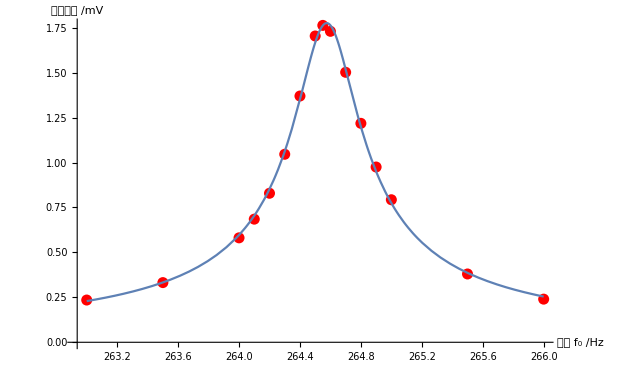

```mathematica
Show[ListPlot[%81,PlotStyle->Red],Plot[{A/(ω0 √(1+Q^2 (ω/ω0-ω0/ω)^2))}/.{A->469.7972951908664,Q->643.3690658888073,ω0->264.57537402826335},{ω,263.,266.}],AxesLabel->{"频率 f_0\n/Hz","相对振幅\n/mV"}]
```

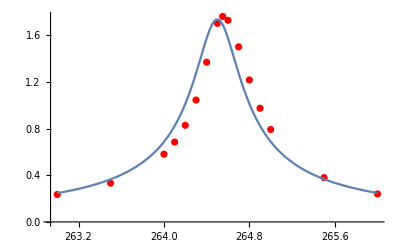

```mathematica
Show[ListPlot[%81,PlotStyle->Red],Plot[{A/(ω0 √(1+Q^2 (ω/ω0-ω0/ω)^2))/.ω0->264.5}/.{A->459.38580045694084,Q->613.2210639277819},{ω,263.,266.}]]
```

```mathematica
Union[Range[260.,262.,1.],Range[262.,263.,.1],{262.55},Range[263.,265.,1.]]
```

{260.,261.,262.,262.1,262.2,262.3,262.4,262.5,262.55,262.6,262.7,262.8,262.9,263.,264.,265.}

```mathematica
{.151,.234,.563,.656,.783,.954,1.185,1.398,1.444,1.438,1.306,1.118,.933,.779,.246,.136}
```

{0.151,0.234,0.563,0.656,0.783,0.954,1.185,1.398,1.444,1.438,1.306,1.118,0.933,0.779,0.246,0.136}

```mathematica
Transpose@{%132,%134}
```

{{260.,0.151},{261.,0.234},{262.,0.563},{262.1,0.656},{262.2,0.783},{262.3,0.954},{262.4,1.185},{262.5,1.398},{262.55,1.444},{262.6,1.438},{262.7,1.306},{262.8,1.118},{262.9,0.933},{263.,0.779},{264.,0.246},{265.,0.136}}

```mathematica
FindFit[%135,{A/(ω0 √(1+Q^2(ω/ω0-ω0/ω)^2)),262<ω0<263,Q>0},{A,Q,ω0},ω]
```

{A→382.186,Q→519.373,ω0→262.587}

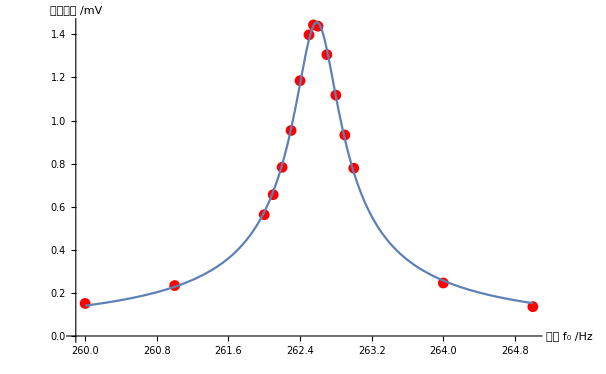

```mathematica
Show[ListPlot[%135,PlotStyle->Red],Plot[{A/(ω0 √(1+Q^2 (ω/ω0-ω0/ω)^2))}/.{A->382.18616562807875,Q->519.3731479488918,ω0->262.5869671910727},{ω,260.,265.}],AxesLabel->{"频率 f_0\n/Hz","相对振幅\n/mV"}]
```